```mathematica
Integrate[Tanh[x],{x,0,1}]
```

Log[Cosh[1]]

```mathematica
Integrate[Sqrt[Coth[x]],{x,0,1}]
```

π/2+ArcCoth[√Coth[1]]-ArcTan[√Coth[1]]

```mathematica
Series[Cos[θ],{θ,0,2}]
```

1-θ^2/2+O[θ]^3

```mathematica
Assuming[{a>0,-a<θ<a},Integrate[Sqrt[1/(2*(1/2*a^2-1/2*θ^2))],θ]//FullSimplify]
```

ArcTan[θ/(√(a^2-θ^2))]

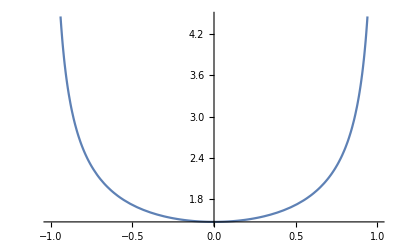

```mathematica
Plot[1/Sqrt[Cos[θ]-Cos[1]],{θ,-1,1}]
```

```mathematica
D[ArcCos[1+Cos[a]-x^2],x]
```

(2 x)/(√(1-(1-x^2+Cos[a])^2))

```mathematica
N[Integrate[1/(Pi*Sqrt[2*(Cos[θ]-Cos[11Pi/12])]),{θ,-11Pi/12,11Pi/12}]]
```

2.18544

```mathematica
Limit[Sqrt[1-x^2]*Sqrt[Cos[θ*x]-Cos[θ]],x->1]
```

0

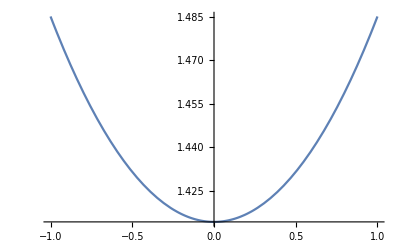

```mathematica
Plot[Sqrt[1-x^2]/Sqrt[Cos[θ*x]-Cos[θ]]/.θ->Pi/3,{x,-1,1}]
```

```mathematica
Assuming[0<θ<Pi,Limit[Sqrt[1-x^2]/Sqrt[Cos[θ*x]-Cos[θ]],x->1]]
```

Indeterminate

```mathematica
N[%]
```

1.63808

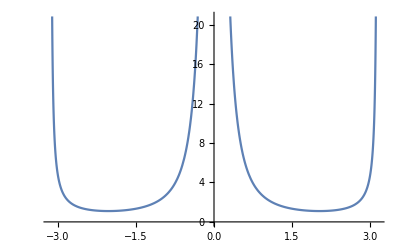

```mathematica
Plot[Limit[(1-x^2)/(Cos[θ*x]-Cos[θ]),x->1],{θ,-Pi,Pi}]
```

```mathematica
Assuming[0<θ<Pi,Limit[Sqrt[(1-x^2)/(Cos[θ*x]-Cos[θ])],x->1]]
```

√2 √(Csc[θ]/θ)

```mathematica
Assuming[0<θ<Pi,Limit[(1-x^2)/(Cos[θ*x]-Cos[θ]),x->-1]]
```

(2 Csc[θ])/θ

```mathematica
%-2/(θ*Sin[θ])
```

0

```mathematica
a=Pi/3;
NIntegrate[1/Sqrt[Cos[θ]-Cos[a]],{θ,-a,a}]/(Pi*Sqrt[2])
NIntegrate[a/Sqrt[Cos[a*x]-Cos[a]],{x,-1,1}]/(Pi*Sqrt[2])
```

1.07318

1.07318

```mathematica
Table[NumberForm[Re[NIntegrate[1/(Pi*Sqrt[2*(Cos[θ]-Cos[a])]),{θ,-a,a},AccuracyGoal->Infinity]],30],{a,Pi/12*Range[11]}]
```

{1.004300572166438,1.017408790466781,1.039973339336188,1.073181999488621,1.118959037463299,1.180340594425067,1.262211619759275,1.372880489784419,1.527947581547658,1.762203727208658,2.185443629799353}